```mathematica
NLODEs = {D[x[t],t] == V0 + V1 β - V2  + V3 + kf y[t] - k x[t],D[y[t],t]== V2 - V3 - kf y[t], D[z[t],t] ==  β V4 - V5 - ϵ z[t]}/.{V2->VM2 x[t]^2/(k2^2 + x[t]^2),V3-> VM3 x[t]^m/(kx^m + x[t]^m)y[t]^2/(ky^2 + y[t]^2)z[t]^4/(kz^4 + z[t]^4),V5->VM5 z[t]^p/(k5^p + z[t]^p)x[t]^n/(kd^n + x[t]^n)}
```

{x'[t]==V0+V1 β-k x[t]-(VM2 x[t]^2)/(k2^2+x[t]^2)+kf y[t]+(VM3 x[t]^m y[t]^2 z[t]^4)/((kx^m+x[t]^m) (ky^2+y[t]^2) (kz^4+z[t]^4)),y'[t]==(VM2 x[t]^2)/(k2^2+x[t]^2)-kf y[t]-(VM3 x[t]^m y[t]^2 z[t]^4)/((kx^m+x[t]^m) (ky^2+y[t]^2) (kz^4+z[t]^4)),z'[t]==V4 β-ϵ z[t]-(VM5 x[t]^n z[t]^p)/((kd^n+x[t]^n) (k5^p+z[t]^p))}

```mathematica
tmax = 20;
```

### Steady State

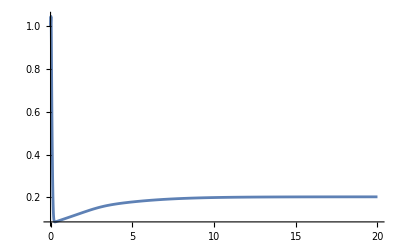

```mathematica
VvalsSS = {V0->2,V1->2 , V4->5, kf->1,k->10,β-> 0.01,ϵ->0.1 ,VM2->6,k2->0.1,VM3->20,m->2,kx->0.5,ky->0.2,kz->0.2,VM5->30,k5->0.3,kd->0.5,p->2,n->4};
solSS= NDSolve[Join[NLODEs/.VvalsSS,{x[0]==1,y[0]==1,z[0]==1}],{x[t],y[t],z[t]},{t,0,tmax}];
Plot[x[t]/.solSS[[1]],{t,0,tmax},PlotRange->All]
```

### Simple Periodic Oscillations

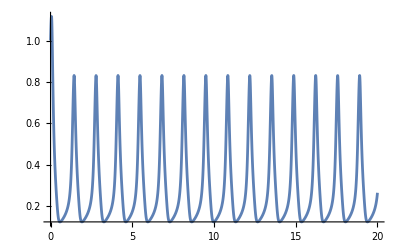

```mathematica
VvalsSPO = {V0->2,V1->2 , V4->2, kf->1,k->10,β-> 0.5,ϵ->0.1 ,VM2->6,k2->0.1,VM3->20,m->2,kx->0.5,ky->0.2,kz->0.2,VM5->5,k5->1,kd->0.4,p->2,n->4};
solSPO = NDSolve[Join[NLODEs/.VvalsSPO,{x[0]==1,y[0]==1,z[0]==1}],{x[t],y[t],z[t]},{t,0,tmax}];
Plot[x[t]/.solSPO[[1]],{t,0,tmax},PlotRange->All]
```

### Bursting

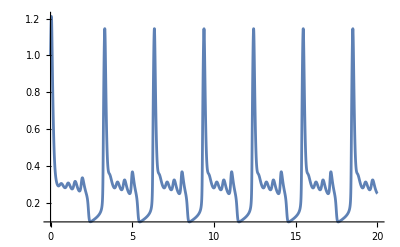

```mathematica
VvalsB = {V0->2,V1->2 , V4->2.5, kf->1,k->10,β-> 0.46,ϵ->0.1 ,VM2->6,k2->0.1,VM3->20,m->4,kx->0.3,ky->0.2,kz->0.1,VM5->30,k5->1,kd->0.6,p->1,n->2};
solB = NDSolve[Join[NLODEs/.VvalsB,{x[0]==1,y[0]==1,z[0]==1}],{x[t],y[t],z[t]},{t,0,tmax}];
Plot[x[t]/.solB[[1]],{t,0,tmax},PlotRange->All]
```

### Chaos

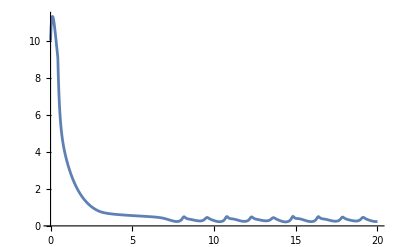

```mathematica
VvalsC= {V0->2,V1->2 , V4->3, kf->1,k->10,β-> 0.65,ϵ->13 ,VM2->6,k2->0.1,VM3->30,m->2,kx->0.6,ky->0.3,kz->0.1,VM5->50,k5->0.3194,kd->1,p->1,n->4};
solC = NDSolve[Join[NLODEs/.VvalsC,{x[0]==10,y[0]==100,z[0]==1000}],{x[t],y[t],z[t]},{t,0,tmax}];
Plot[x[t]/.solC[[1]],{t,0,tmax},PlotRange->All]
```

### Period Doubling Sequences

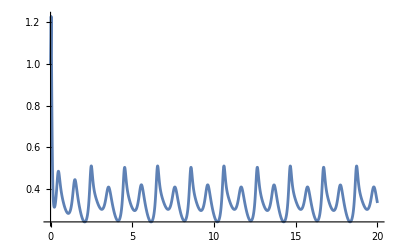

```mathematica
VvalsPDS= {V0->2,V1->2 , V4->3, kf->1,k->10,β-> 0.7,ϵ->13 ,VM2->6,k2->0.1,VM3->30,m->2,kx->0.6,ky->0.3,kz->0.1,VM5->50,k5->0.3194,kd->1,p->1,n->4};
solPDS = NDSolve[Join[NLODEs/.VvalsPDS,{x[0]==1,y[0]==1,z[0]==1}],{x[t],y[t],z[t]},{t,0,tmax}];
Plot[x[t]/.solPDS[[1]],{t,0,tmax},PlotRange->All]
```